Import map

```mathematica
$map=Import[$HomeDirectory<>"/Sites/EMPREP/Maps/11x17map.jan2017.jpg"]
$dim=ImageDimensions[$map]
```

-Graphics-

{1700,2550}

Interpolate pixel locations [lat,long]

{{Hilgard Ave=2777=,-122.256,37.8796,1392,1140},{Le Conte Ave=2634=,-122.258,37.877,156,2300},{Buena Vista Way=2750=,-122.257,37.8812,814,206},{Le Roy Ave=1597=,-122.259,37.8799,202,722},{Hilgard Ave=2805=,-122.255,37.8788,1486,1576},{Virginia St=2701=,-122.257,37.8784,768,1636},{La Vereda Rd=1732=,-122.255,37.8779,1279,2014},{La Vereda Rd=1591=,-122.257,37.8802,1018,724},{Hilgard Ave=2650=,-122.258,37.8787,241,1367}}

{{{-122.256,37.8796},1392},{{-122.258,37.877},156},{{-122.257,37.8812},814},{{-122.259,37.8799},202},{{-122.255,37.8788},1486},{{-122.257,37.8784},768},{{-122.255,37.8779},1279},{{-122.257,37.8802},1018},{{-122.258,37.8787},241}}

InterpolatingFunction[{{-122.259, -122.255}, {37.877, 37.8812}}, <>]

{-122.256,-122.258,-122.257,-122.259,-122.255,-122.257,-122.255,-122.257,-122.258}

-122.259

-122.255

{37.8796,37.877,37.8812,37.8799,37.8788,37.8784,37.8779,37.8802,37.8787}

37.877

37.8812

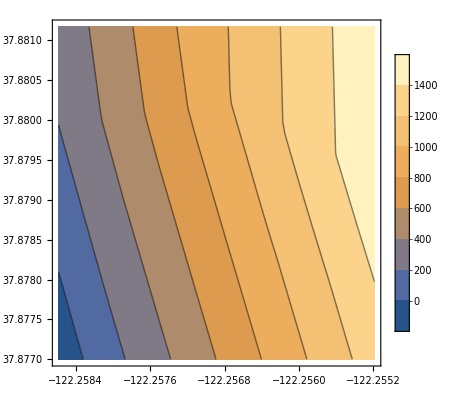

{{{-122.256,37.8796},1140},{{-122.258,37.877},2300},{{-122.257,37.8812},206},{{-122.259,37.8799},722},{{-122.255,37.8788},1576},{{-122.257,37.8784},1636},{{-122.255,37.8779},2014},{{-122.257,37.8802},724},{{-122.258,37.8787},1367}}

InterpolatingFunction[{{-122.259, -122.255}, {37.877, 37.8812}}, <>]

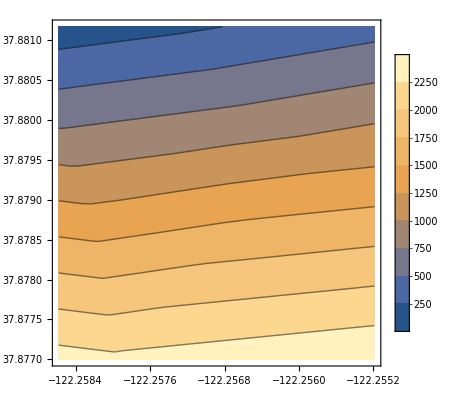

```mathematica
$base=$0=$={{"Hilgard Ave=2777=",-122.25562807,37.87958284,1392,1140},{"Le Conte Ave=2634=",-122.25797414,37.87699862,156,2300},{"Buena Vista Way=2750=",-122.25727989,37.88117325,814,206},{"Le Roy Ave=1597=",-122.25858214,37.87994496,202,722},{"Hilgard Ave=2805=",-122.25518845,37.8787627,1486,1576},{"Virginia St=2701=",-122.25684764,37.8784446,768,1636},{"La Vereda Rd=1732=",-122.25545232, 37.87785934,1279,2014},{"La Vereda Rd=1591=",-122.25668856,37.8802276,1018,724},
{"Hilgard Ave=2650=",-122.2582013,37.87872158,241,1367}
}
$px0=$=Map[{{#[[2]],#[[3]]},#[[4]]}&,$0]
$ipx=Interpolation[$]
$mm=Map[#[[1,1]]&,$]
$mmX0=Min[$mm]
$mmX1=Max[$mm]
$mm=Map[#[[1,2]]&,$]
$mmY0=Min[$mm]
$mmY1=Max[$mm]
ContourPlot[$ipx[x,y],{x,$mmX0,$mmX1},{y,$mmY0,$mmY1},PlotLegends->Automatic]
$py0=$=Map[{{#[[2]],#[[3]]},#[[5]]}&,$0]
$ipy=Interpolation[$]
ContourPlot[$ipy[x,y],{x,$mmX0,$mmX1},{y,$mmY0,$mmY1},PlotLegends->Automatic]
```

Append pixel locations to AddressLL items

```mathematica
($basepx=Map[{$pxaddress[#[[1]]]={#[[4]],#[[5]]}}&,$base])//Column
$baseAddress=Map[#[[1]]&,$base]
$stream=OpenRead[$HomeDirectory<>"/Sites/EMPREP/ICSTool/PL/Lists/MapStreetAddressLL.txt"];
While[($0=ReadLine[$stream] )=!=EndOfFile,
$=StringSplit[$0,"\t"];
If[!MemberQ[$baseAddress,$address=$[[1]]],Continue[]];
$lat=ToExpression[$[[2]]];
$lon=ToExpression[$[[3]]];
$px=$ipx[$lat,$lon];
$py=$ipy[$lat,$lon];
$=$0<>"\t"<>ToString[$px]<>"\t"<>ToString[$py];
Print[$," ",$pxaddress[$address]];
WriteLine[$ostream,$];
]
```

{{1392,1140}}
{{156,2300}}
{{814,206}}
{{202,722}}
{{1486,1576}}
{{768,1636}}
{{1279,2014}}
{{1018,724}}
{{241,1367}}

{Hilgard Ave=2777=,Le Conte Ave=2634=,Buena Vista Way=2750=,Le Roy Ave=1597=,Hilgard Ave=2805=,Virginia St=2701=,La Vereda Rd=1732=,La Vereda Rd=1591=,Hilgard Ave=2650=}

Buena Vista Way=2750=	-122.25727989	37.88117325	814.	206. {814,206}

Le Conte Ave=2634=	-122.25797414	37.87699862	156.	2300. {156,2300}

Le Roy Ave=1597=	-122.25858214	37.87994496	202.	722. {202,722}

Hilgard Ave=2650=	-122.2582013	37.87872158	241.	1367. {241,1367}

Hilgard Ave=2805=	-122.25518845	37.8787627	1486.	1576. {1486,1576}

Hilgard Ave=2777=	-122.25562807	37.87958284	1392.	1140. {1392,1140}

La Vereda Rd=1732=	-122.25545232	37.87785934	1279.	2014. {1279,2014}

La Vereda Rd=1591=	-122.25668856	37.8802276	1018.	724. {1018,724}

Virginia St=2701=	-122.25684764	37.8784446	768.	1636. {768,1636}

```mathematica
$dim
```

{1700,2550}

```mathematica
$stream=OpenRead[$HomeDirectory<>"/Sites/EMPREP/ICSTool/PL/Lists/MapStreetAddressLL.txt"];
(*Close[$ostream]*)$ostream=OpenWrite[$HomeDirectory<>"/Sites/EMPREP/ICSTool/PL/Lists/MapStreetAddressLLpx.txt"];
$pix={};
While[($0=ReadLine[$stream] )=!=EndOfFile,
$=StringSplit[$0,"\t"];
$address=$[[1]];
$lat=ToExpression[$[[2]]];
$lon=ToExpression[$[[3]]];
$px=$ipx[$lat,$lon];
$py=$ipy[$lat,$lon];
$=$0<>"\t"<>ToString[$px]<>"\t"<>ToString[$py];
WriteLine[$ostream,$];
If[MemberQ[$baseAddress,$address],Print[$,"⇒",$pxaddress[$address]]];
AppendTo[$pix,{$px,$dim[[2]]-$py}];
];
```

Buena Vista Way=2750=	-122.25727989	37.88117325	814.	206.⇒{814,206}

Le Conte Ave=2634=	-122.25797414	37.87699862	156.	2300.⇒{156,2300}

Le Roy Ave=1597=	-122.25858214	37.87994496	202.	722.⇒{202,722}

Hilgard Ave=2650=	-122.2582013	37.87872158	241.	1367.⇒{241,1367}

Hilgard Ave=2805=	-122.25518845	37.8787627	1486.	1576.⇒{1486,1576}

Hilgard Ave=2777=	-122.25562807	37.87958284	1392.	1140.⇒{1392,1140}

La Vereda Rd=1732=	-122.25545232	37.87785934	1279.	2014.⇒{1279,2014}

La Vereda Rd=1591=	-122.25668856	37.8802276	1018.	724.⇒{1018,724}

Virginia St=2701=	-122.25684764	37.8784446	768.	1636.⇒{768,1636}

Check pixel locations on map

```mathematica
ImageCompose[$map,Graphics[{Red,PointSize[.01],Point[$pix]},Frame->True,PlotRange->{{0,1700},{0,2550}}]]
```

-Graphics-